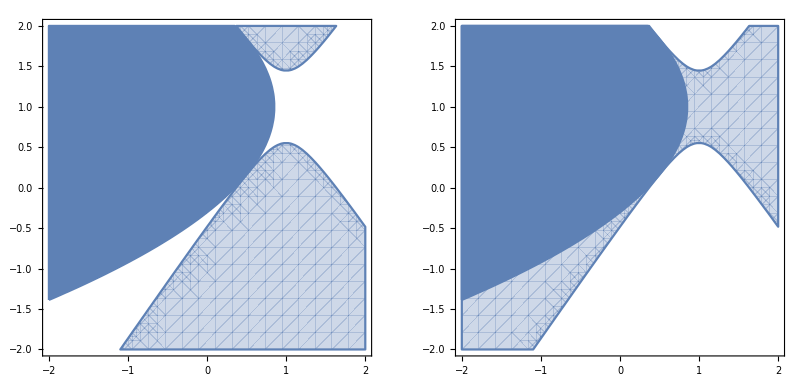

```mathematica
u =0.5;
q[x_]:=(x-1)^2;
lq[x_,u_]:=q[u]+q'[u]*(x-u);
lq[x,0.5];
plt1  =Show[RegionPlot[lq[x,0.5] - 0.5*q[y]> -0.1,{x,-2,2},{y,-2,2}, PlotStyle->"Red"], RegionPlot[q[x] - 0.5*q[y]> -0.1,{x,-2,2},{y,-2,2} ]];
plt2  = Show[RegionPlot[lq[x,0.5] - 0.5*q[y]> -0.1,{x,-2,2},{y,-2,2}, PlotStyle->"Red"], RegionPlot[q[x] - 0.5*q[y]< -0.1,{x,-2,2},{y,-2,2} ]];
GraphicsRow[{plt2,plt1}]
```